# Lab 11: Onset of Chaos

## Exploring the Theory

The logistic equation

x_(n+1) = ax_n (1- x_n )

maps scenarios like population growth. The function below takes the parameter a and returns a new function that computes one iteration of the map .

```mathematica
logisticMap[a_]:=Function[x,a*x*(1-x)]
```

The NestList function applies the logistic map function repeatedly and gives the entire sequence. It takes parameters a, the growth factor, x_0, the initial population, and n, the number of iterations.

```mathematica
logisticIterations[a_,x0_,n_]:=NestList[logisticMap[a],x0,n]
```

What we should expect for ranges of a is:
-  a < 1: population dies out
- 1 < a < 3: population stabilizes at a single value
- a > 3: population begins to oscillate
- a > 3.57: chaos begins
To demonstrate, we’ll set up some example initial parameters and calculate the results.
Parameters:
	a = 2.8
	x_0 = 0.4
	n = 10

```mathematica
result = logisticIterations[2.8,0.4,10];
TableForm[
Transpose[{Range[0,10], result}],
TableHeadings->{None, {"n", "x(n)"}}
]
```

n | x(n)
0 | 0.4
1 | 0.672
2 | 0.617165
3 | 0.661563
4 | 0.626913
5 | 0.654901
6 | 0.632816
7 | 0.650608
8 | 0.636489
9 | 0.647838
10 | 0.638803

Since 1<a<3, the population stabilizes at a fixed point near 0.64. Next, let’s model the behavior when a>3.

```mathematica
result = logisticIterations[3.2,0.4,20];
TableForm[
Transpose[{Range[0,20], result}],
TableHeadings->{None, {"n", "x(n)"}}
]
```

n | x(n)
0 | 0.4
1 | 0.768
2 | 0.570163
3 | 0.784247
4 | 0.541452
5 | 0.794502
6 | 0.52246
7 | 0.798386
8 | 0.515091
9 | 0.799271
10 | 0.513398
11 | 0.799426
12 | 0.513102
13 | 0.799451
14 | 0.513054
15 | 0.799455
16 | 0.513046
17 | 0.799455
18 | 0.513045
19 | 0.799455
20 | 0.513045

The results show the population begins to oscillate between ~ 0.5 and 0.8. Now, let’s calculate the population behavior when a>3.57.

```mathematica
result = logisticIterations[3.7,0.4,20];
TableForm[
Transpose[{Range[0,20], result}],
TableHeadings->{None, {"n", "x(n)"}}
]
```

n | x(n)
0 | 0.4
1 | 0.888
2 | 0.367987
3 | 0.860519
4 | 0.444097
5 | 0.913437
6 | 0.292558
7 | 0.765781
8 | 0.663633
9 | 0.82593
10 | 0.531948
11 | 0.921223
12 | 0.268512
13 | 0.726729
14 | 0.734797
15 | 0.72102
16 | 0.744256
17 | 0.704255
18 | 0.770636
19 | 0.653997
20 | 0.837254

The population now fluctuates with no easily discernable pattern.

### Plots

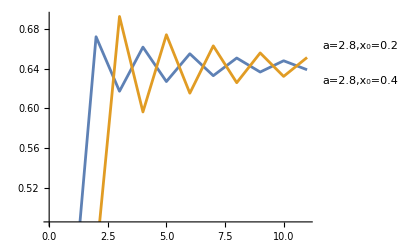

```mathematica
ListLinePlot[{Labeled[
logisticIterations[2.8,0.4,10],"a=2.8,x_0=0.4"],
Labeled[logisticIterations[2.8,0.2,10],"a=2.8,x_0=0.2"]}]
```

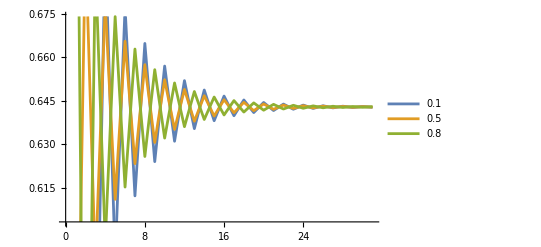

```mathematica
ListLinePlot[{logisticIterations[2.8,0.1,30],logisticIterations[2.8,0.5,30],logisticIterations[2.8,.8,30]},PlotLegends->{0.1, 0.5, 0.8}]
```

Figure X: Logistic map with a = 2.8 and x_0 = {0.1,0.5, 0.8}

Plot a = 0.5 with with 3 values of x_0.

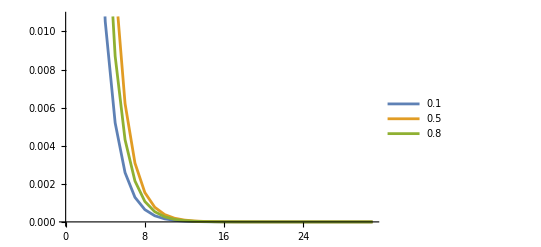

```mathematica
ListLinePlot[{logisticIterations[0.5, 0.1, 30], logisticIterations[0.5, 0.5, 30], logisticIterations[0.5, .8, 30]}, PlotLegends -> {0.1, 0.5, 0.8}]
```

Figure X: When a < 1, we expect this population to die out.We observe this here, 
where all 3 curves go to zero.

Plot a = 1

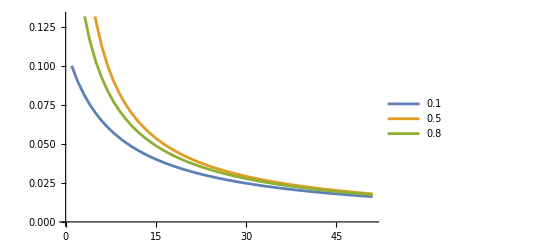

```mathematica
ListLinePlot[{
logisticIterations[1, 0.1, 50],
logisticIterations[1, 0.5, 50], 
logisticIterations[1, .8, 50]
}, PlotLegends -> {0.1, 0.5, 0.8}]
```

Figure X: When a = 1, we expect this population to to be on the borderline between
stabilizing at a point and dying out,

a = 1.5

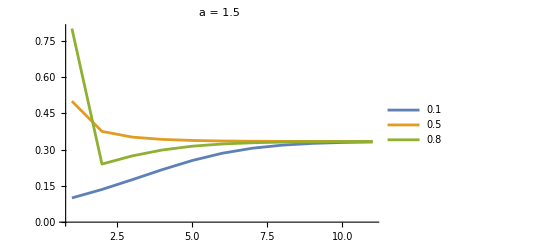

```mathematica
ListLinePlot[{
logisticIterations[1.5, 0.1, 10],
logisticIterations[1.5, 0.5, 10], 
logisticIterations[1.5, .8, 10]
}, PlotLegends -> {0.1, 0.5, 0.8},PlotRange->All,PlotLabel->"a = 1.5"]
```

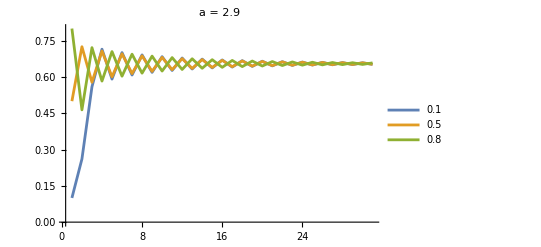

```mathematica
ListLinePlot[{
logisticIterations[2.9, 0.1, 30],
logisticIterations[2.9, 0.5, 30], 
logisticIterations[2.9, .8, 30]
}, PlotLegends -> {0.1, 0.5, 0.8},PlotRange->All,PlotLabel->"a = 2.9"]
```

```mathematica
ListLinePlot[
{
Labeled[logisticIterations[3.01, 0.5, 700],"x0 = 0.5"],
Labeled[logisticIterations[3.01, 0.667, 700],"x0 = 0.667"]
},
PlotLayout->"Row",
PlotLabel->"a = 3.01",
PlotRange->All
]
```

-Graphics-

```mathematica
ListLinePlot[
{
Labeled[logisticIterations[2.99, 0.5, 400],"x0 = 0.5"],
Labeled[logisticIterations[2.99, 0.667, 400],"x0 = 0.667"]
},
PlotLayout->"Row",
PlotLabel->"a = 2.99",
PlotRange->All
]
```

-Graphics-

Clustering note: periodicity? FFT? Shifting?

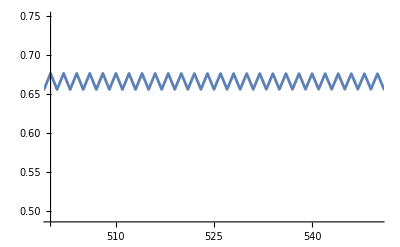

```mathematica
ListLinePlot[logisticIterations[3,0.5,1000],PlotRange->{{500,550},All}]
```